Chapter 14 Radiation by Moving Charges - G

```mathematica
Clear[ω,ω0,q,ρ,γ,γθ,θ]
ω0=1;
q=1;
ρ=1/ω0;
γ=1;
γθ = γ θ;
ξ=(ω ρ)/3(1/γ^2+θ^2)^1.5;
```

1

```mathematica
dI2d0dO=Function[ {θ,ω,γ1},1/(3 π^2)(ω ρ)^2(1/γ^2+θ^2)^2 (BesselK[2/3,ξ]^2+θ^2/(1/γ^2+θ^2)BesselK[1/3,ξ]^2)]
```

Function[{θ,ω,γ1},((ω ρ)^2 (1/γ^2+θ^2)^2 (BesselK[2/3,ξ]^2+(θ^2 BesselK[1/3,ξ]^2)/(1/γ^2+θ^2)))/(3 π^2)]

Figure 14.11

```mathematica
F=Function[y,(9√3)/(8 π)y NIntegrate[BesselK[5/3,x],{x,y,100*y}]]
```

Function[y,((9 √3) y NIntegrate[BesselK[5/3,x],{x,y,100 y}])/(8 π)]

```mathematica
y=Table[y,{y,0.01,10,0.05}];
Fy=Table[F[y],{y,0.01,10,0.05}];
```

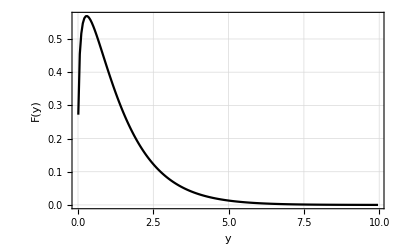

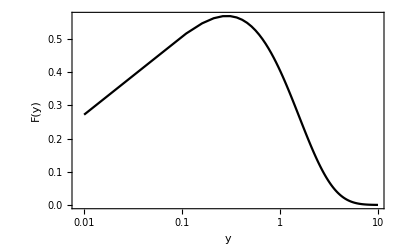

```mathematica
ListPlot[Transpose[{y,Fy}],PlotTheme->"Detailed",PlotStyle->Black,FrameLabel->{"y","F(y)"},Joined->True]

ListLogLinearPlot[Transpose[{y,Fy}],PlotTheme->"Detailed",PlotStyle->Black,FrameLabel->{"y","F(y)"},Joined->True]
```